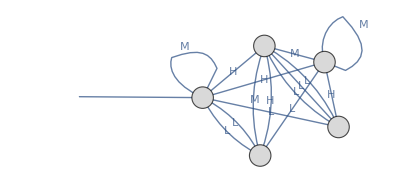

```mathematica
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
RandomAuGraph=
Graph[{-1->2,
Labeled[0->1,"L"],Labeled[0->0,"M"],Labeled[0->2,"H"],
Labeled[1->2,"L"],Labeled[1->3,"M"],Labeled[1->2,"H"],
Labeled[2->4,"L"],Labeled[2->2,"M"],Labeled[2->3,"H"],
Labeled[3->4,"L"],Labeled[3->0,"M"],Labeled[3->1,"H"],
Labeled[4->3,"L"],Labeled[4->3,"M"],Labeled[4->0,"H"]},
EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],
VertexStyle->LightGray,
VertexShapeFunction->VertexCircle,
VertexLabels->{0->Placed["L",Center],1->Placed["H",Center],2->Placed["L",Center], 3->Placed["H",Center],4->Placed["M",Center]}
];
G=Graphics[{White,Disk[{0,.5},.2]}];
S=Show[RandomAuGraph,G]
(*Export["random.svg",S]*)
```

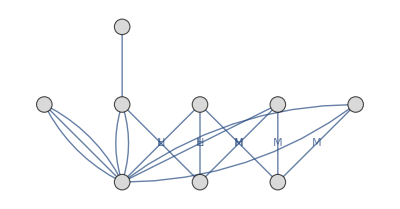

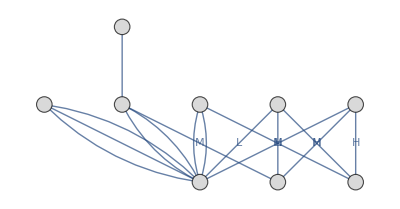

```mathematica
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
a0Graph=Graph[{-1->0,Labeled[0->L,M,"L"],Labeled[0->L,M,"M"],Labeled[0->H,"H"],Labeled[1->L,"L"],Labeled[1->M,"M"],Labeled[1->H,"H"],Labeled[2->L,"L"],Labeled[2->M,"M"],Labeled[2->H,"H"],Labeled[3->L,H,"L"],Labeled[3->M,"M"],Labeled[3->L,H,"H"],Labeled[4->L,M,H,"L"],Labeled[4->L,M,H,"M"],Labeled[4->L,M,H,"H"]},EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],VertexStyle->LightGray,VertexShapeFunction->VertexCircle,VertexLabels->{0->Placed["L",Center],1->Placed["M",Center],2->Placed["H",Center]}];
a0Graph
(*Export["a0.png",a0Graph];*)
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
a1Graph=Graph[{-1->1,Labeled[0->L,"L"],Labeled[0->M,"M"],Labeled[0->H,"H"],Labeled[1->L,M,"L"],Labeled[1->L,M,"M"],Labeled[1->H,"H"],Labeled[2->L,"L"],Labeled[2->M,"M"],Labeled[2->H,"H"],Labeled[3->L,"L"],Labeled[3->M,"M"],Labeled[3->H,"H"],Labeled[4->L,"L"],Labeled[4->M,H,"M"],Labeled[4->M,H,"H"]},EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],VertexStyle->LightGray,VertexShapeFunction->VertexCircle,VertexLabels->{0->Placed["L",Center],1->Placed["M",Center],2->Placed["H",Center]}];
(*Export["a1.png",a1Graph];*)
```

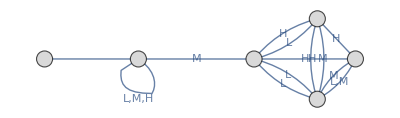

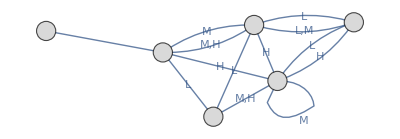

```mathematica
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
a0Graph=Graph[{-1->3,Labeled[0->1,"L,M"],Labeled[0->4,"H"],Labeled[1->4,"L"],Labeled[1->0,"M"],Labeled[1->2,"H"],Labeled[2->4,"L"],Labeled[2->1,"M"],Labeled[2->0,"H"],Labeled[3->3,"L,M,H"],Labeled[4->1,"L"],Labeled[4->3,"M"],Labeled[4->2,"H"]},EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],VertexStyle->LightGray,VertexShapeFunction->VertexCircle,VertexLabels->{0->Placed["M",Center],1->Placed["M",Center],2->Placed["M",Center],3->Placed["M",Center],4->Placed["L",Center]}];
a0Graph
(*Export["a0.png",a0Graph];*)
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
a1Graph=Graph[{-1->4,Labeled[0->1,"L"],Labeled[0->3,"M,H"],Labeled[1->2,"L"],Labeled[1->4,"M,H"],Labeled[2->1,"L,M"],Labeled[2->3,"H"],Labeled[3->2,"L"],Labeled[3->3,"M"],Labeled[3->1,"H"],Labeled[4->0,"L"],Labeled[4->1,"M"],Labeled[4->3,"H"]},EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],VertexStyle->LightGray,VertexShapeFunction->VertexCircle,VertexLabels->{0->Placed["M",Center],1->Placed["H",Center],2->Placed["M",Center],3->Placed["L",Center],4->Placed["M",Center]}];
a1Graph
(*Export["a1.png",a1Graph];*)
```

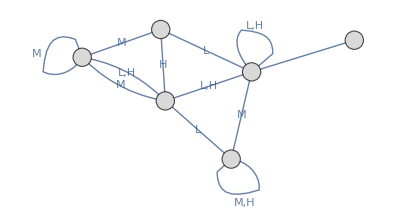

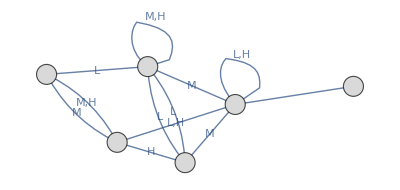

```mathematica
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
a0Graph=Graph[{-1->2,Labeled[0->3,"L,H"],Labeled[0->0,"M"],Labeled[1->2,"L"],Labeled[1->0,"M"],Labeled[1->3,"H"],Labeled[2->2,"L,H"],Labeled[2->4,"M"],Labeled[3->2,"L,H"],Labeled[3->0,"M"],Labeled[4->3,"L"],Labeled[4->4,"M,H"]},EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],VertexStyle->LightGray,VertexShapeFunction->VertexCircle,VertexLabels->{0->Placed["H",Center],1->Placed["L",Center],2->Placed["M",Center],3->Placed["M",Center],4->Placed["M",Center]}];
a0Graph
(*Export["a0.png",a0Graph];*)
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
a1Graph=Graph[{-1->2,Labeled[0->4,"L"],Labeled[0->2,"M"],Labeled[0->3,"H"],Labeled[1->4,"L"],Labeled[1->3,"M,H"],Labeled[2->2,"L,H"],Labeled[2->4,"M"],Labeled[3->2,"L,H"],Labeled[3->1,"M"],Labeled[4->0,"L"],Labeled[4->4,"M,H"]},EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],VertexStyle->LightGray,VertexShapeFunction->VertexCircle,VertexLabels->{0->Placed["H",Center],1->Placed["L",Center],2->Placed["M",Center],3->Placed["M",Center],4->Placed["M",Center]}];
a1Graph
(*Export["a1.png",a1Graph];*)
```

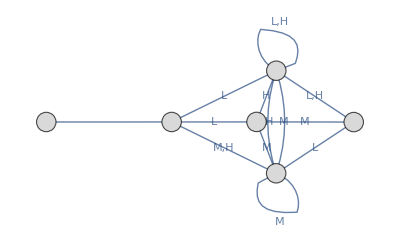

```mathematica
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
a1Graph=Graph[{-1->3,Labeled[0->3,"L"],Labeled[0->2,"M"],Labeled[0->4,"H"],Labeled[1->4,"L,H"],Labeled[1->0,"M"],Labeled[2->1,"L"],Labeled[2->2,"M"],Labeled[2->4,"H"],Labeled[3->4,"L"],Labeled[3->2,"M,H"],Labeled[4->4,"L,H"],Labeled[4->2,"M"]},EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],VertexStyle->LightGray,VertexShapeFunction->VertexCircle,VertexLabels->{0->Placed["L",Center],1->Placed["H",Center],2->Placed["M",Center],3->Placed["H",Center],4->Placed["M",Center]}];
a1Graph
```

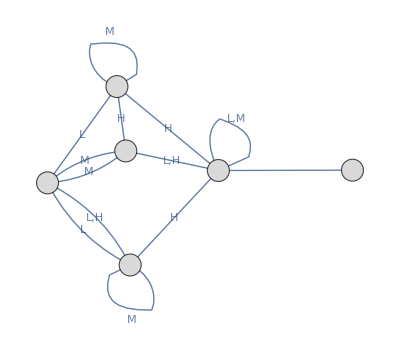

```mathematica
VertexCircle[{xc_,yc_},name_,{w_,h_}]:=Disk[{xc,yc},.1];
a1Graph=Graph[{-1->4,Labeled[0->2,"L,H"],Labeled[0->1,"M"],Labeled[1->4,"L,H"],Labeled[1->0,"M"],Labeled[2->0,"L"],Labeled[2->2,"M"],Labeled[2->4,"H"],Labeled[3->0,"L"],Labeled[3->3,"M"],Labeled[3->1,"H"],Labeled[4->4,"L,M"],Labeled[4->3,"H"]},EdgeShapeFunction->GraphElementData["EdgeShapeFunction","FilledArrow"],VertexStyle->LightGray,VertexShapeFunction->VertexCircle,VertexLabels->{0->Placed["H",Center],1->Placed["L",Center],2->Placed["M",Center],3->Placed["M",Center],4->Placed["H",Center]}];
a1Graph
(*Export["a1.png",a1Graph];*)
```